# XPS Data Processing

## 2021-03-15

Rule number 1: Press ctrl-s obsessively. I had a beautifully worded introduction here that I lost because Mathematica crashed. I’ll try to recreate it, but this is just a tribute.

This file represents the start of a paradigm shift in how I approach my scientific data processing. I’ll be the first to admit that I go through this process too often. I think that my data processing code isn’t well organized and is difficult to understand, so I’ll commit a full half day to changing it, only to find that it’s pretty much the same thing as what I had before and in another 2 months I’ll want to go through the same process again. This time will be different. Why? In part because of this file. This is a Mathematica Notebook but I’m treating it more like a notebook in the traditional “lab notebook” sense. Text that I write here will remain after it is written. Cells will be edited only if they result in insignificant errors. If it’s a learning opportunity, I’ll leave the error in there and write about why it occurred and how I think I’ll fix it.

As I reach usable code, the code will be transferred to a separate script or package file that I will use version control on. This way, I can always be sure to be able to analyze the data in exactly the same way that I did initially, even if I change the code later to improve it in some way, or change the way that the data is recorded, or something.

```mathematica
SetDirectory[FileNameJoin[{$DATARUNS,"2021-03-15","data"}]]
FileNames[]
```

C:\Users\kahrendsen2\Box Sync\Gay Group\Project - Rb Spin Filter\karl\DataRuns\2021-03-15\data

{Au120sAged.xls,Au240s.xls,Au60s.xls,AuPreVacuum.xls,C0s.xls,C240s.xls,C60s.xls,formvar60s.xls}

```mathematica
Import["Au120sAged.xls"]
```

{{{,,,,,,,Acquisition Parameters :,,,,,Experiment Descriptions :},{,,,,,,,,,,,,  },{,,,,,,,Parameter, ,,,,Experiment\X-Ray011 400um - FG  ON\Au 120 s Aged},{,,,,,,,Total acquisition time,27.8 secs,,,,},{,,,,,,,Number of Scans,5.,,,,},{,,,,,,,Source Gun Type,Al K Alpha,,,,},115,{81.58,,38023.8,,,,,,,,,,},{81.48,,36713.7,,,,,,,,,,},{81.38,,35788.3,,,,,,,,,,},{81.28,,36207.3,,,,,,,,,,},{81.18,,35045.7,,,,,,,,,,},{81.08,,34982.5,,,,,,,,,,}},7,{{}}}
 |  |  |  |

```mathematica
im=%
```

{{{,,,,,,,Acquisition Parameters :,,,,,Experiment Descriptions :},{,,,,,,,,,,,,  },{,,,,,,,Parameter, ,,,,Experiment\X-Ray011 400um - FG  ON\Au 120 s Aged},{,,,,,,,Total acquisition time,27.8 secs,,,,},{,,,,,,,Number of Scans,5.,,,,},{,,,,,,,Source Gun Type,Al K Alpha,,,,},115,{81.58,,38023.8,,,,,,,,,,},{81.48,,36713.7,,,,,,,,,,},{81.38,,35788.3,,,,,,,,,,},{81.28,,36207.3,,,,,,,,,,},{81.18,,35045.7,,,,,,,,,,},{81.08,,34982.5,,,,,,,,,,}},7,{{}}}
 |  |  |  |

```mathematica
(* Just import the sheet names? *)
fn="Au120sAged.xls"
sn=Import[fn,"Sheets"](* sn = Sheet Names *)
```

Au120sAged.xls

{Au4f Scan,Na1s Scan,O1s Scan,N1s Scan,C1s Scan,S2p Scan,Peak Table,Titles,Sheet1}

```mathematica
(* Just import the gold data based on the sheet name *)
Import[fn,{sn[[1]]}]
```

Import::noelem: The Import element "Au4f Scan" is not present when importing as XLS.

$Failed

```mathematica
(* I think I have to specify that I want to import the "Data" element first.*)
ri=Import[fn,{"Data",sn[[1]]}](* ri = (R)aw (I)mport *)
```

{{,,,,,,,Acquisition Parameters :,,,,,Experiment Descriptions :},{,,,,,,,,,,,,  },{,,,,,,,Parameter, ,,,,Experiment\X-Ray011 400um - FG  ON\Au 120 s Aged},{,,,,,,,Total acquisition time,27.8 secs,,,,},{,,,,,,,Number of Scans,5.,,,,},{,,,,,,,Source Gun Type,Al K Alpha,,,,},{Axis,Energy,Elements=,111.,,,,Spot Size,400 µm,,,,},{,,,,,,,Lens Mode,Standard,,,,},{C:\Users\expert\Desktop\User data 2021\Ahrendsen\cysteineMultipleExposures\Experiment\X-Ray011 400um - FG  ON\Au 120 s Aged\Au4f Scan.VGD,,,,,,,Analyser Mode,CAE : Pass Energy 50.0 eV,,,,},{,,,,,,,Energy Step Size,0.100 eV,,,,},{,,,,,,,Number of Energy Steps,111.,,,,},{,,,,,,,,,,,,},{,,,,,,,,,,,,},{,,,,,,,,,,,,},{Binding Energy (E),,,,,,,,,,,,},{eV,,Counts / s,,,,,,,,,,},{92.08,,102001.,,,,,,,,,,},{91.98,,102787.,,,,,,,,,,},{91.88,,102706.,,,,,,,,,,},{91.78,,103571.,,,,,,,,,,},{91.68,,105603.,,,,,,,,,,},{91.58,,106420.,,,,,,,,,,},{91.48,,107323.,,,,,,,,,,},{91.38,,110144.,,,,,,,,,,},{91.28,,109995.,,,,,,,,,,},{91.18,,111388.,,,,,,,,,,},{91.08,,113061.,,,,,,,,,,},{90.98,,113587.,,,,,,,,,,},{90.88,,114653.,,,,,,,,,,},{90.78,,116765.,,,,,,,,,,},{90.68,,115620.,,,,,,,,,,},{90.58,,116516.,,,,,,,,,,},{90.48,,119144.,,,,,,,,,,},{90.38,,118177.,,,,,,,,,,},{90.28,,120997.,,,,,,,,,,},{90.18,,122364.,,,,,,,,,,},{90.08,,125047.,,,,,,,,,,},{89.98,,126648.,,,,,,,,,,},{89.88,,129543.,,,,,,,,,,},{89.78,,134421.,,,,,,,,,,},{89.68,,141073.,,,,,,,,,,},{89.58,,148304.,,,,,,,,,,},{89.48,,155469.,,,,,,,,,,},{89.38,,166625.,,,,,,,,,,},{89.28,,184097.,,,,,,,,,,},{89.18,,205058.,,,,,,,,,,},{89.08,,234200.,,,,,,,,,,},{88.98,,280305.,,,,,,,,,,},{88.88,,342659.,,,,,,,,,,},{88.78,,433886.,,,,,,,,,,},{88.68,,557714.,,,,,,,,,,},{88.58,,697253.,,,,,,,,,,},{88.48,,833614.,,,,,,,,,,},{88.38,,931991.,,,,,,,,,,},{88.28,,961807.,,,,,,,,,,},{88.18,,903461.,,,,,,,,,,},{88.08,,796545.,,,,,,,,,,},{87.98,,663466.,,,,,,,,,,},{87.88,,530422.,,,,,,,,,,},{87.78,,420126.,,,,,,,,,,},{87.68,,336652.,,,,,,,,,,},{87.58,,274450.,,,,,,,,,,},{87.48,,230752.,,,,,,,,,,},{87.38,,200114.,,,,,,,,,,},{87.28,,176921.,,,,,,,,,,},{87.18,,161632.,,,,,,,,,,},{87.08,,151710.,,,,,,,,,,},{86.98,,141304.,,,,,,,,,,},{86.88,,134624.,,,,,,,,,,},{86.78,,129504.,,,,,,,,,,},{86.68,,126554.,,,,,,,,,,},{86.58,,124120.,,,,,,,,,,},{86.48,,122757.,,,,,,,,,,},{86.38,,122265.,,,,,,,,,,},{86.28,,122515.,,,,,,,,,,},{86.18,,125830.,,,,,,,,,,},{86.08,,128428.,,,,,,,,,,},{85.98,,133565.,,,,,,,,,,},{85.88,,142514.,,,,,,,,,,},{85.78,,152419.,,,,,,,,,,},{85.68,,166809.,,,,,,,,,,},{85.58,,185325.,,,,,,,,,,},{85.48,,212983.,,,,,,,,,,},{85.38,,254355.,,,,,,,,,,},{85.28,,314535.,,,,,,,,,,},{85.18,,405304.,,,,,,,,,,},{85.08,,532803.,,,,,,,,,,},{84.98,,701837.,,,,,,,,,,},{84.88,,890647.,,,,,,,,,,},{84.78,,1.06778×10^6,,,,,,,,,,},{84.68,,1.17693×10^6,,,,,,,,,,},{84.58,,1.19081×10^6,,,,,,,,,,},{84.48,,1.09476×10^6,,,,,,,,,,},{84.38,,933288.,,,,,,,,,,},{84.28,,748131.,,,,,,,,,,},{84.18,,575196.,,,,,,,,,,},{84.08,,436345.,,,,,,,,,,},{83.98,,332706.,,,,,,,,,,},{83.88,,257199.,,,,,,,,,,},{83.78,,202166.,,,,,,,,,,},{83.68,,163311.,,,,,,,,,,},{83.58,,136534.,,,,,,,,,,},{83.48,,117028.,,,,,,,,,,},{83.38,,101366.,,,,,,,,,,},{83.28,,91101.7,,,,,,,,,,},{83.18,,82084.1,,,,,,,,,,},{83.08,,74431.6,,,,,,,,,,},{82.98,,68843.7,,,,,,,,,,},{82.88,,64255.3,,,,,,,,,,},{82.78,,59661.3,,,,,,,,,,},{82.68,,55553.1,,,,,,,,,,},{82.58,,53703.5,,,,,,,,,,},{82.48,,50690.5,,,,,,,,,,},{82.38,,48178.4,,,,,,,,,,},{82.28,,45588.,,,,,,,,,,},{82.18,,44513.2,,,,,,,,,,},{82.08,,43182.3,,,,,,,,,,},{81.98,,41664.6,,,,,,,,,,},{81.88,,40197.8,,,,,,,,,,},{81.78,,39698.7,,,,,,,,,,},{81.68,,38713.1,,,,,,,,,,},{81.58,,38023.8,,,,,,,,,,},{81.48,,36713.7,,,,,,,,,,},{81.38,,35788.3,,,,,,,,,,},{81.28,,36207.3,,,,,,,,,,},{81.18,,35045.7,,,,,,,,,,},{81.08,,34982.5,,,,,,,,,,}}

```mathematica
(* Playing around a bit here to find where the actual data starts and *)
jd =ri[[17;;]] (* jd = (J)ust (D)ata *)
(* Picking out just the columsn with numbers that we want *)
op=jd[[All,{1,3}]] (* op= (O)rdered (P)airs, these are the things that can be directly plotted. Kinda want to have a better name for these *)
```

{{92.08,,102001.,,,,,,,,,,},{91.98,,102787.,,,,,,,,,,},{91.88,,102706.,,,,,,,,,,},{91.78,,103571.,,,,,,,,,,},{91.68,,105603.,,,,,,,,,,},{91.58,,106420.,,,,,,,,,,},{91.48,,107323.,,,,,,,,,,},{91.38,,110144.,,,,,,,,,,},{91.28,,109995.,,,,,,,,,,},{91.18,,111388.,,,,,,,,,,},{91.08,,113061.,,,,,,,,,,},{90.98,,113587.,,,,,,,,,,},{90.88,,114653.,,,,,,,,,,},{90.78,,116765.,,,,,,,,,,},{90.68,,115620.,,,,,,,,,,},{90.58,,116516.,,,,,,,,,,},{90.48,,119144.,,,,,,,,,,},{90.38,,118177.,,,,,,,,,,},{90.28,,120997.,,,,,,,,,,},{90.18,,122364.,,,,,,,,,,},{90.08,,125047.,,,,,,,,,,},{89.98,,126648.,,,,,,,,,,},{89.88,,129543.,,,,,,,,,,},{89.78,,134421.,,,,,,,,,,},{89.68,,141073.,,,,,,,,,,},{89.58,,148304.,,,,,,,,,,},{89.48,,155469.,,,,,,,,,,},{89.38,,166625.,,,,,,,,,,},{89.28,,184097.,,,,,,,,,,},{89.18,,205058.,,,,,,,,,,},{89.08,,234200.,,,,,,,,,,},{88.98,,280305.,,,,,,,,,,},{88.88,,342659.,,,,,,,,,,},{88.78,,433886.,,,,,,,,,,},{88.68,,557714.,,,,,,,,,,},{88.58,,697253.,,,,,,,,,,},{88.48,,833614.,,,,,,,,,,},{88.38,,931991.,,,,,,,,,,},{88.28,,961807.,,,,,,,,,,},{88.18,,903461.,,,,,,,,,,},{88.08,,796545.,,,,,,,,,,},{87.98,,663466.,,,,,,,,,,},{87.88,,530422.,,,,,,,,,,},{87.78,,420126.,,,,,,,,,,},{87.68,,336652.,,,,,,,,,,},{87.58,,274450.,,,,,,,,,,},{87.48,,230752.,,,,,,,,,,},{87.38,,200114.,,,,,,,,,,},{87.28,,176921.,,,,,,,,,,},{87.18,,161632.,,,,,,,,,,},{87.08,,151710.,,,,,,,,,,},{86.98,,141304.,,,,,,,,,,},{86.88,,134624.,,,,,,,,,,},{86.78,,129504.,,,,,,,,,,},{86.68,,126554.,,,,,,,,,,},{86.58,,124120.,,,,,,,,,,},{86.48,,122757.,,,,,,,,,,},{86.38,,122265.,,,,,,,,,,},{86.28,,122515.,,,,,,,,,,},{86.18,,125830.,,,,,,,,,,},{86.08,,128428.,,,,,,,,,,},{85.98,,133565.,,,,,,,,,,},{85.88,,142514.,,,,,,,,,,},{85.78,,152419.,,,,,,,,,,},{85.68,,166809.,,,,,,,,,,},{85.58,,185325.,,,,,,,,,,},{85.48,,212983.,,,,,,,,,,},{85.38,,254355.,,,,,,,,,,},{85.28,,314535.,,,,,,,,,,},{85.18,,405304.,,,,,,,,,,},{85.08,,532803.,,,,,,,,,,},{84.98,,701837.,,,,,,,,,,},{84.88,,890647.,,,,,,,,,,},{84.78,,1.06778×10^6,,,,,,,,,,},{84.68,,1.17693×10^6,,,,,,,,,,},{84.58,,1.19081×10^6,,,,,,,,,,},{84.48,,1.09476×10^6,,,,,,,,,,},{84.38,,933288.,,,,,,,,,,},{84.28,,748131.,,,,,,,,,,},{84.18,,575196.,,,,,,,,,,},{84.08,,436345.,,,,,,,,,,},{83.98,,332706.,,,,,,,,,,},{83.88,,257199.,,,,,,,,,,},{83.78,,202166.,,,,,,,,,,},{83.68,,163311.,,,,,,,,,,},{83.58,,136534.,,,,,,,,,,},{83.48,,117028.,,,,,,,,,,},{83.38,,101366.,,,,,,,,,,},{83.28,,91101.7,,,,,,,,,,},{83.18,,82084.1,,,,,,,,,,},{83.08,,74431.6,,,,,,,,,,},{82.98,,68843.7,,,,,,,,,,},{82.88,,64255.3,,,,,,,,,,},{82.78,,59661.3,,,,,,,,,,},{82.68,,55553.1,,,,,,,,,,},{82.58,,53703.5,,,,,,,,,,},{82.48,,50690.5,,,,,,,,,,},{82.38,,48178.4,,,,,,,,,,},{82.28,,45588.,,,,,,,,,,},{82.18,,44513.2,,,,,,,,,,},{82.08,,43182.3,,,,,,,,,,},{81.98,,41664.6,,,,,,,,,,},{81.88,,40197.8,,,,,,,,,,},{81.78,,39698.7,,,,,,,,,,},{81.68,,38713.1,,,,,,,,,,},{81.58,,38023.8,,,,,,,,,,},{81.48,,36713.7,,,,,,,,,,},{81.38,,35788.3,,,,,,,,,,},{81.28,,36207.3,,,,,,,,,,},{81.18,,35045.7,,,,,,,,,,},{81.08,,34982.5,,,,,,,,,,}}

{{92.08,102001.},{91.98,102787.},{91.88,102706.},{91.78,103571.},{91.68,105603.},{91.58,106420.},{91.48,107323.},{91.38,110144.},{91.28,109995.},{91.18,111388.},{91.08,113061.},{90.98,113587.},{90.88,114653.},{90.78,116765.},{90.68,115620.},{90.58,116516.},{90.48,119144.},{90.38,118177.},{90.28,120997.},{90.18,122364.},{90.08,125047.},{89.98,126648.},{89.88,129543.},{89.78,134421.},{89.68,141073.},{89.58,148304.},{89.48,155469.},{89.38,166625.},{89.28,184097.},{89.18,205058.},{89.08,234200.},{88.98,280305.},{88.88,342659.},{88.78,433886.},{88.68,557714.},{88.58,697253.},{88.48,833614.},{88.38,931991.},{88.28,961807.},{88.18,903461.},{88.08,796545.},{87.98,663466.},{87.88,530422.},{87.78,420126.},{87.68,336652.},{87.58,274450.},{87.48,230752.},{87.38,200114.},{87.28,176921.},{87.18,161632.},{87.08,151710.},{86.98,141304.},{86.88,134624.},{86.78,129504.},{86.68,126554.},{86.58,124120.},{86.48,122757.},{86.38,122265.},{86.28,122515.},{86.18,125830.},{86.08,128428.},{85.98,133565.},{85.88,142514.},{85.78,152419.},{85.68,166809.},{85.58,185325.},{85.48,212983.},{85.38,254355.},{85.28,314535.},{85.18,405304.},{85.08,532803.},{84.98,701837.},{84.88,890647.},{84.78,1.06778×10^6},{84.68,1.17693×10^6},{84.58,1.19081×10^6},{84.48,1.09476×10^6},{84.38,933288.},{84.28,748131.},{84.18,575196.},{84.08,436345.},{83.98,332706.},{83.88,257199.},{83.78,202166.},{83.68,163311.},{83.58,136534.},{83.48,117028.},{83.38,101366.},{83.28,91101.7},{83.18,82084.1},{83.08,74431.6},{82.98,68843.7},{82.88,64255.3},{82.78,59661.3},{82.68,55553.1},{82.58,53703.5},{82.48,50690.5},{82.38,48178.4},{82.28,45588.},{82.18,44513.2},{82.08,43182.3},{81.98,41664.6},{81.88,40197.8},{81.78,39698.7},{81.68,38713.1},{81.58,38023.8},{81.48,36713.7},{81.38,35788.3},{81.28,36207.3},{81.18,35045.7},{81.08,34982.5}}

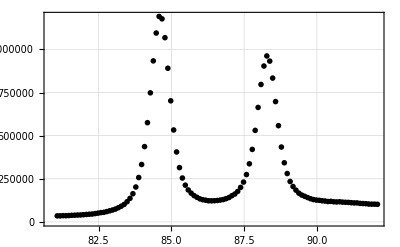

```mathematica
ListPlot[{op}]
```

Okay! I think we’ve mostly got something usable here. I’m going to go back and copy the necessary lines to put this all in one cell.

```mathematica
fn="Au120sAged.xls";
sn="S2p Scan";
(* Need to specify that we want the "Data" from the excel sheet, rather than the sheetnames or some other metadata.*)
ri=Import[fn,{"Data",sn}];(* ri = (R)aw (I)mport *)
jd =ri[[17;;]];(* jd = (J)ust (D)ata *)
op=jd[[All,{1,3}]] (* op= (O)rdered (P)airs *)
```

{{174.08,122278.},{173.98,122186.},{173.88,122847.},{173.78,122325.},{173.68,122412.},{173.58,122798.},{173.48,122224.},{173.38,122861.},{173.28,121563.},{173.18,122441.},{173.08,122640.},{172.98,122510.},{172.88,122285.},{172.78,122721.},{172.68,122755.},{172.58,122200.},{172.48,122493.},{172.38,122111.},{172.28,122442.},{172.18,122621.},{172.08,123259.},{171.98,122911.},{171.88,123442.},{171.78,123248.},{171.68,122282.},{171.58,123003.},{171.48,123562.},{171.38,123899.},{171.28,122731.},{171.18,123321.},{171.08,124171.},{170.98,123339.},{170.88,123960.},{170.78,124561.},{170.68,124959.},{170.58,124721.},{170.48,125449.},{170.38,125131.},{170.28,125520.},{170.18,125900.},{170.08,126255.},{169.98,126020.},{169.88,126033.},{169.78,126338.},{169.68,126183.},{169.58,127161.},{169.48,127213.},{169.38,127700.},{169.28,127833.},{169.18,127762.},{169.08,127615.},{168.98,127984.},{168.88,127770.},{168.78,127750.},{168.68,127608.},{168.58,127320.},{168.48,126763.},{168.38,127192.},{168.28,126528.},{168.18,125922.},{168.08,125983.},{167.98,125587.},{167.88,124856.},{167.78,124797.},{167.68,125358.},{167.58,124856.},{167.48,125480.},{167.38,125442.},{167.28,124414.},{167.18,124423.},{167.08,124047.},{166.98,124227.},{166.88,124025.},{166.78,124461.},{166.68,123813.},{166.58,124822.},{166.48,124216.},{166.38,124935.},{166.28,124792.},{166.18,124313.},{166.08,124465.},{165.98,124234.},{165.88,124092.},{165.78,124117.},{165.68,124295.},{165.58,124742.},{165.48,123843.},{165.38,123954.},{165.28,124656.},{165.18,124044.},{165.08,124472.},{164.98,124915.},{164.88,124883.},{164.78,124326.},{164.68,124429.},{164.58,124636.},{164.48,124689.},{164.38,125144.},{164.28,125791.},{164.18,124970.},{164.08,125372.},{163.98,125558.},{163.88,125444.},{163.78,126504.},{163.68,125412.},{163.58,125466.},{163.48,125403.},{163.38,125599.},{163.28,125719.},{163.18,126180.},{163.08,126367.},{162.98,126025.},{162.88,125861.},{162.78,125955.},{162.68,126510.},{162.58,125437.},{162.48,126680.},{162.38,126246.},{162.28,126235.},{162.18,126375.},{162.08,126340.},{161.98,126201.},{161.88,126259.},{161.78,126138.},{161.68,126299.},{161.58,126311.},{161.48,125971.},{161.38,126293.},{161.28,125793.},{161.18,125430.},{161.08,125328.},{160.98,125149.},{160.88,125382.},{160.78,125397.},{160.68,125267.},{160.58,125544.},{160.48,124845.},{160.38,125601.},{160.28,125907.},{160.18,126220.},{160.08,125580.}}

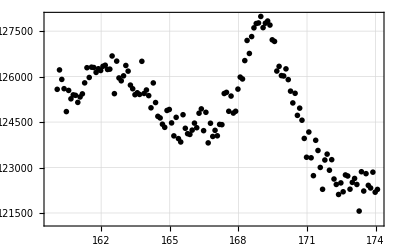

```mathematica
ListPlot[{op}]
```

Binding energy plots are typically plotted with BE increasing to the LEFT rather than the right, there should be an option in ListPlot to flip this.

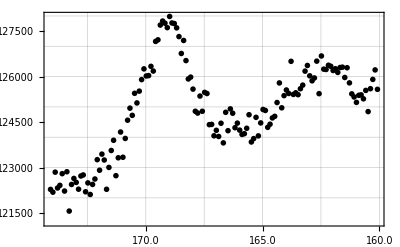

```mathematica
ListPlot[{op},ScalingFunctions->{"Reverse","Linear"}]
```

Okay, so I should now be able to make the above into a function where I provide a list of OP of files and sheet names as input and receive as output a list of ordered pairs.

```mathematica
ExtractXPSData[fn_String(*fileName *),sn_String(* Sheet name *)]:=Module[
{ri,jd,op,lds,dc},
(* Need to specify that we want the "Data" from the excel sheet, rather than the sheetnames or some other metadata.*)
ri=Import[fn,{"Data",sn}];(* ri = (R)aw (I)mport *)
lds=17;(* The (l)ine the (d)ata (s)tarts on *)
jd =ri[[lds;;]];(* jd = (J)ust (D)ata *)
dc={1,3};(* (d)ata (c)olumns  *)
op=jd[[All,dc]] (* op= (O)rdered (P)airs *)
]
SetAttributes[ExtractXPSData,Listable]
```

```mathematica
FileNames[]
```

{Au120sAged.xls,Au240s.xls,Au60s.xls,AuPreVacuum.xls,C0s.xls,C240s.xls,C60s.xls,formvar60s.xls}

```mathematica
fn={"AuPreVacuum.xls","Au60s.xls","Au120sAged.xls","Au240s.xls"};
op=ExtractXPSData[fn,sn];
ListPlot[op,ScalingFunctions->{"Reverse","Linear"},PlotLabels->{"0s","60s","120s","240s"}]
```

-Graphics-

Okay, now I need to do some re-scaling so that we can more clearly see how the datasets compare. Let’s first try just subtracting the intensity value of the right-most datapoint from each set.

```mathematica
NormalizeRightSubtract[data_]:=Apply[{#1,#2-data[[-1,2]]}&,data,{1}];
ClearAttributes[NormalizeRightSubtract,Listable]
```

```mathematica
norm1=Map[NormalizeRightSubtract,op];
```

```mathematica
ListPlot[norm1,ScalingFunctions->{"Reverse","Linear"},PlotLabels->{"0s","60s","120s","240s"}]
```

-Graphics-

It doesn’t look super great. What if we instead subtract the left-most intensity?

```mathematica
NormalizeLeftSubtract[data_]:=Apply[{#1,#2-data[[1,2]]}&,data,{1}];
norm2=Map[NormalizeLeftSubtract,op];
ListPlot[norm2,ScalingFunctions->{"Reverse","Linear"},PlotLabels->{"0s","60s","120s","240s"}]
```

-Graphics-

Not much better. Let’s take a moving average.

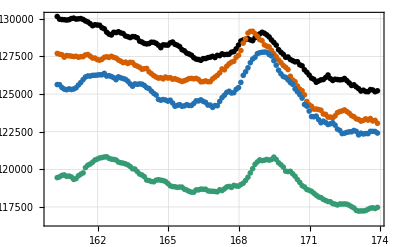

```mathematica
ma=Map[MovingAverage[#,5]&,op];
ListPlot[ma]
```

It’s not obviously better. As a final try, let’s remove a slope from the data.

```mathematica
Clear[NormalizeSlopeSubtract]
NormalizeSlopeSubtract[data_]:=Module[
{rise,run,slope,temp},
{run,rise}=data[[-1]]-data[[1]];
slope=Echo[rise/run];
temp=Apply[{#1,(#2-slope*#1)/data[[-1,2]]}&,data,{1}];
Apply[{#1,#2-temp[[-1,2]]}&,temp,{1}]
];
ClearAttributes[NormalizeSlopeSubtract,Listable]
```

```mathematica
norm3=Map[NormalizeSlopeSubtract,op];
ListPlot[norm3,ScalingFunctions->{"Reverse","Linear"},PlotLabels->{"0s","60s","120s","240s"},Joined->True]
```

-340.

-331.

-235.857

-125.143

-Graphics-

As another alternative (which I think is probably most accurate) let’s normalize to the peak.

```mathematica
Clear[NormalizeToPeak]
NormalizeToPeak[data_]:=Module[
{peak},
peak=Max[Transpose[data][[2]]];
Apply[{#1,#2/Max[peak]}&,data,{1}]
];
ClearAttributes[NormalizeToPeak,Listable]
```

```mathematica
norm3=Map[NormalizeSlopeSubtract,op];
norm4=Map[NormalizeToPeak,norm3];
ListPlot[norm4,ScalingFunctions->{"Reverse","Linear"},PlotLabels->{"0s","60s","120s","240s"},Joined->True]
```

-340.

-331.

-235.857

-125.143

0.

0.

0.

«1 more identical outputs»

-Graphics-

```mathematica
OffsetDataVertically[data_,offset_]:=Apply[{#1,#2+offset}&,data,{1}];
```

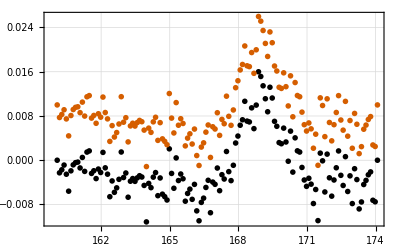

```mathematica
ListPlot[{norm3[[1]],OffsetDataVertically[norm3[[1]],.01]}]
```

None of these is really as convincing as looking at each of the plots individually on their own scale.

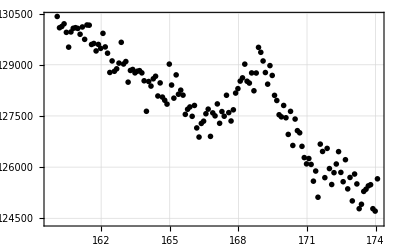
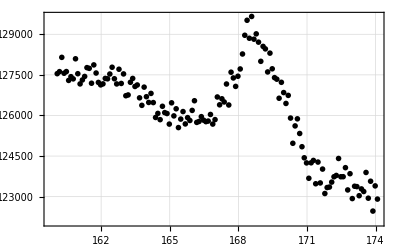
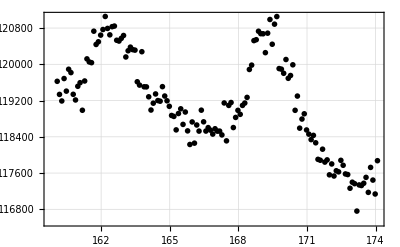
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[ListPlot[{#}]&,op]
```